{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→10,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

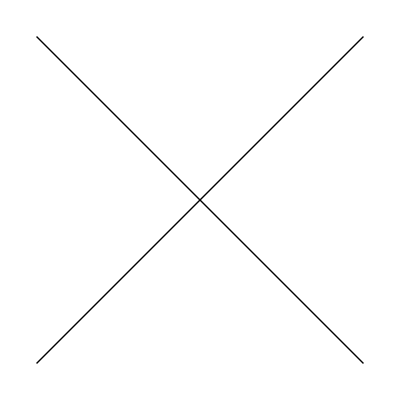
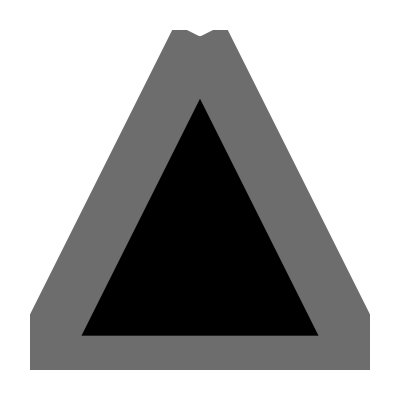
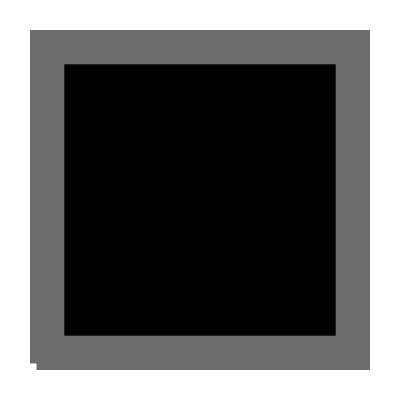
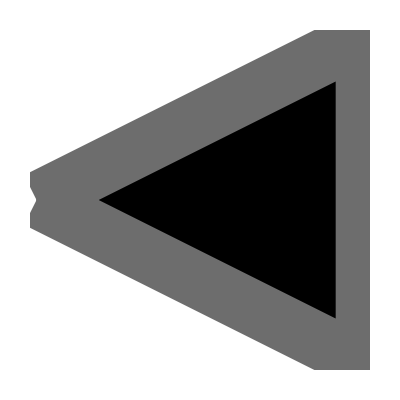
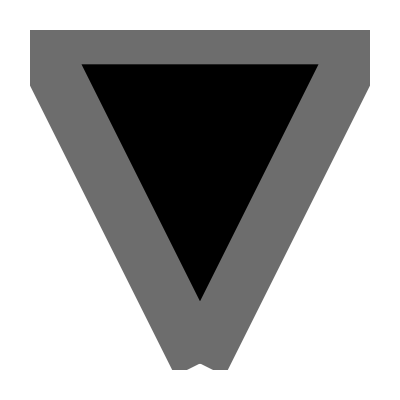
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
<<MaTeX`
myblue=RGBColor[0.2745098039,0.5333333333,0.9450980392];
myred=RGBColor[0.9176470588,0.2588235294,0.2078431373];
mygreen=RGBColor[0.2039215686,0.662745098,0.3176470588];
myyellow=RGBColor[0.9764705882,0.7333333333,0.1764705882];
mygray=RGBColor[109/255//N,109/255//N,109/255//N];
mylightgray=RGBColor[185/255//N,185/255//N,185/255//N];
thickness=0.005;
size=0.05;
font="Latin Modern Roman";
imagSize=200;
fontSize=10;
markersize=0.025;
cm=72/2.54;

SetOptions[MaTeX,FontSize->fontSize]
SetOptions[MatrixPlot,FrameTicksStyle->Black,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],ImageSize->imagSize,AspectRatio->1];
SetOptions[ListPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}},Joined->True];
SetOptions[ListPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}},Joined->True];
SetOptions[ListDensityPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black];
SetOptions[Plot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}}];
SetOptions[DensityPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black];
align = Sequence[AlignmentPoint -> {0, 0}, AxesOrigin -> {0, 0}, BaselinePosition -> Axis];
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
plotRangePadding = .01;
edgeThickness = .1;
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
halfTr = {Graphics[{EdgeForm[{mygray, Thickness[edgeThickness], JoinForm["Round"]}], Line[{{-1, -1}, {1, 1}}], Line[{{-1, 1}, {1, -1}}](*EdgeForm[],FaceForm[Opacity[1]],Polygon[{{0,2},{2/Sqrt[3],0},{-(2/Sqrt[3]),0}}],EdgeForm[{Opacity[1],Thickness[edgeThickness],JoinForm["Round"]}],FaceForm[],Polygon[{{0,2},{Sqrt[3],-1},{-Sqrt[3],-1}}]*)}, align],
   Graphics[{EdgeForm[{mygray, Thickness[edgeThickness], JoinForm["Round"]}], Polygon[{{0, 1}, {1, -1}, {-1, -1}}]}, align],
   Graphics[{EdgeForm[{mygray, Thickness[edgeThickness], JoinForm["Round"]}], Rectangle[{-1, -1}, {1, 1}]}, align]};
halfTr = Flatten[{halfTr, Table[halfTr /. p : {_?NumericQ, _?NumericQ} :> RotationMatrix[θ].p, {θ, {Pi/2,  Pi}}]}, 2] /. "size" -> size
Magnify[#, .1] & /@ halfTr;
ListPlot[Flatten[Table[{{n, y}}, {y, Range[1, 3]}, {n, 20}], 1], PlotMarkers -> Table[{s, 0.07}, {s, halfTr}], PlotStyle -> ColorData[60, "ColorList"], GridLines -> {Range[20], Range[3]}, PlotRange -> {{0, 21}, {0, 4}}, Axes -> False, Frame -> True];

new={{"GoogleGradient","",{}},{"Gradients"},1,{0,1},{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred},""};
ColorData["GoogleGradient"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];

new={{"GoogleGradientRev","",{}},{"Gradients"},1,{0,1},Reverse[{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred}],""};
ColorData["GoogleGradientRev"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];

new={{"GoogleGradientWhiteRed","",{}},{"Gradients"},1,{0,1},{White,myred},""};
ColorData["GoogleGradientWhiteRed"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];

new={{"GoogleGradientWhiteBlue","",{}},{"Gradients"},1,{0,1},{myblue,White},""};
ColorData["GoogleGradientWhiteBlue"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
```

```mathematica
(* The Hamiltonian in momentum space as defined in the main text *)
Clear[Uderiv,h0,hx,hz,h,hzh,hxh,uu,vv,m,g,χ,k]
h0[χ_,k_]=-Cos[k]*Cos[χ/2];
hx[m_,g_,k_]=m-g Cos[k];
hz[χ_,k_]=Sin[k]Sin[χ/2];
h[m_,g_,χ_,k_]=√(hx[m,g,k]^2+hz[χ,k]^2);

hzh[m_,g_,χ_,k_]=hz[χ,k]/h[m,g,χ,k];
hxh[m_,g_,χ_,k_]=hx[m,g,k]/h[m,g,χ,k];

uu[m_,g_,χ_,k_]=1/(√2)√(1+hzh[m,g,χ,k]);
vv[m_,g_,χ_,k_]=+Sign[hx[m,g,k]]/(√2)√(1-hzh[m,g,χ,k]);
vv0[m_,g_,χ_,k_]=+1/(√2)√(1-hzh[m,g,χ,k]);

bands[m_,g_,χ_,k_]:=h0[χ,k]*{1,1}+√(hx[m,g,k]^2+hz[χ,k]^2)*{1,-1};
vF[m_,g_,χ_,k_]=D[bands[m,g,χ,k],k];
aF[m_,g_,χ_,k_]=D[vF[m,g,χ,k],k];
U[m_,g_,χ_,k_]=(IdentityMatrix[2]*uu[m,g,χ,k] - PauliMatrix[2] ⅈ vv[m,g,χ,k]);
U0[m_,g_,χ_,k_]=(IdentityMatrix[2]*uu[m,g,χ,k] - PauliMatrix[2] ⅈ vv0[m,g,χ,k]);
Uderiv[m_,g_,χ_,k_]=Abs[D[uu[m,g,χ,k],k]];
Uderiv2[m_,g_,χ_,k_]=Abs[D[uu[m,g,χ,k],{k,2}]];
Uderiv3[m_,g_,χ_,k_]=Abs[D[uu[m,g,χ,k],{k,3}]];
Uderiv4[m_,g_,χ_,k_]=Abs[D[uu[m,g,χ,k],{k,4}]];
Uderiv5[m_,g_,χ_,k_]=Abs[D[uu[m,g,χ,k],{k,5}]];
Uderiv6[m_,g_,χ_,k_]=Abs[D[uu[m,g,χ,k],{k,6}]];
Uderiv7[m_,g_,χ_,k_]=Abs[D[uu[m,g,χ,k],{k,7}]];
Uderiv8[m_,g_,χ_,k_]=Abs[D[uu[m,g,χ,k],{k,8}]];
Uderiv9[m_,g_,χ_,k_]=Abs[D[uu[m,g,χ,k],{k,9}]];
Uderiv10[m_,g_,χ_,k_]=Abs[D[uu[m,g,χ,k],{k,10}]];
Vderiv[m_,g_,χ_,k_]=Abs[D[vv0[m,g,χ,k],k]];
Vderiv2[m_,g_,χ_,k_]=Abs[D[vv0[m,g,χ,k],{k,2}]];
Vderiv3[m_,g_,χ_,k_]=Abs[D[vv0[m,g,χ,k],{k,3}]];
Vderiv4[m_,g_,χ_,k_]=Abs[D[vv0[m,g,χ,k],{k,4}]];
Vderiv5[m_,g_,χ_,k_]=Abs[D[vv0[m,g,χ,k],{k,5}]];
(* the argument of the sums in the expression of <Subscript[H, parallel]>, <Subscript[H, perp]> and <Subscript[H, U]> according to first order perturbation theory *)
argPara[m_,g_,χ_,k_,l_]=(1+hzh[m,g,χ,k]*hzh[m,g,χ,l])*(1-Cos[k-l]);
argPerp[m_,g_,χ_,k_,l_]=1-hzh[m,g,χ,k]*hzh[m,g,χ,l]-hxh[m,g,χ,k]*hxh[m,g,χ,l]*Cos[k-l];
argU[m_,g_,χ_,k_,l_]=(1-hzh[m,g,χ,k]*hzh[m,g,χ,l]-hxh[m,g,χ,k]*hxh[m,g,χ,l]);
```

```mathematica
Hkin[m_,g_,χ_,k_]={h0[χ,k],hx[m,g,k],0,hz[χ,k]}.{IdentityMatrix[2],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
(* Hkin is diagonalized with U† Hkin U.*)
mm=1.;
gg=1.;
chi=1.*π;
kk=0.25π;
U[mm,gg,chi,kk]†.Hkin[mm,gg,chi,kk].U[mm,gg,chi,kk]//FullSimplify
```

{{0.765367,-2.77556×10^-17},{-2.77556×10^-17,-0.765367}}

```mathematica
ColorData["GoogleGradient"][0]
```

RGBColor[0.2745098039, 0.5333333333, 0.9450980392]

```mathematica
ths=Thickness[.003];
ts=0.02*{1,1/GoldenRatio};
ticks={{{{0.,MaTeX["0"],ts},{-1,MaTeX["-1"],ts},{-2,MaTeX["-2"],ts},{-3,MaTeX["-3"],ts},{+1,MaTeX["+1"],ts},{+2,MaTeX["+2"],ts},{+3,MaTeX[""],ts},{+3,Rotate[MaTeX["\\epsilon_\\pm(k)"],π/2],0*ts}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{0.,MaTeX["0."],ts},{-1,MaTeX["-1.0"],ts},{-.5,MaTeX["-0.5"],ts},{.5,MaTeX["0.5"],ts}},{{.9,MaTeX["k/\\pi"],.0}}],{None}}};
legend={MaTeX["\\uparrow"],MaTeX["\\downarrow"]}
Manipulate[
pp=
Show[
RegionPlot[bands[m,g,χ,π][[2]]<y<bands[m,g,χ,0][[2]],{x,-1,1},{y,-3,0},BoundaryStyle->None,PlotStyle->{mygray,Opacity[.15]}]
,
RegionPlot[bands[m,g,χ,0][[2]]<y<bands[m,g,χ,π][[2]],{x,-1,1},{y,-3,0},BoundaryStyle->None,PlotStyle->{mygray,Opacity[.15]}]
,
Plot[bands[m,g,χ,k*π][[1]],{k,-1,1},PlotRange->Full,PlotStyle->Thickness[.025],ColorFunction->Function[{x,y},ColorData["GoogleGradient"][Abs[vv[m,g,χ,(x-.5)*2π]]^2]],PlotLegends->Placed[LineLegend[{myblue,myred},legend],{Left,Center}]]
,
Plot[bands[m,g,χ,k*π][[2]],{k,-1,1},PlotRange->Full,PlotStyle->Thickness[.025],ColorFunction->Function[{x,y},ColorData["GoogleGradient"][Abs[uu[m,g,χ,(x-.5)*2π]]^2]]]
,
Plot[bands[m,g,χ,k*π],{k,-1,1},PlotStyle->{Thick,Dashed,Black}]
,
PlotRange->{{-1,1},{-2.,3.5}}
,
PlotRangePadding->0
,
FrameTicks->ticks
,
ImageSize->imagSize
,
ImagePadding->{{20,2},{20,2}}
,
Epilog->
{
Inset[MaTeX["g="<>ToString[NumberForm[gg=N[g],{3,2}]]],{.9,3.},{Right,Bottom}]
,
Inset[MaTeX["\\chi="<>ToString[NumberForm[chi=N[χ/π],{3,2}]]<>"\\pi"],{-.9,3.},{Left,Bottom}]
,
Inset[
ParametricPlot[{hx[mm,gg,k],hz[chi,k]},{k,-π,π},PlotStyle->mygreen,FrameTicks->None,AspectRatio->1,Frame->True,PlotRange->{{-1,3},{-1,1}},AxesOrigin->{0,0},AxesStyle->{{Thin,Dashed},{Thin,Dashed}},ImageSize->50,PlotRangePadding->0,PlotStyle->{Thickness[0.02],Black},FrameLabel->MaTeX[{"h_x","h_z"}]],{-.1,3.4},{Center,Top}]
}
,
GridLines->{{},{}}

]
,{{m,1.0},0,1},{{g,1.5},0,2},{{χ,.5π},0,2π}]
```

{-Graphics-,-Graphics-}

```mathematica
plotBandStructure[m_,g_,χ_]:=Module[{pp},
pp=
Show[
Plot[bands[m,g,χ,k*π][[1]],{k,-1,1},PlotRange->Full,PlotStyle->Thick,ColorFunction->Function[{x,y},ColorData["GoogleGradient"][Abs[vv[m,g,χ,(x-.5)*2π]]^2]],GridLines->None
,
PlotLegends->Placed[LineLegend[{myblue,myred},legend],{Left,Center}]]
,
Plot[bands[m,g,χ,k*π][[2]],{k,-1,1},PlotRange->Full,PlotStyle->Thick,ColorFunction->Function[{x,y},ColorData["GoogleGradient"][Abs[uu[m,g,χ,(x-.5)*2π]]^2]],GridLines->None]
,
Plot[bands[m,g,χ,k*π],{k,-1,1},PlotStyle->{Thin,Dashed,mygray}]
,
PlotRange->{{-1,1},3.5*{-1.,1.}}
,
PlotRangePadding->0
,
FrameLabel->MaTeX[{"k/\\pi","\\epsilon_\\pm"}]
,
Epilog->
{
Inset[MaTeX["m="<>ToString[NumberForm[N[m],{3,2}]]],{0,-2.}]
,
Inset[MaTeX["g="<>ToString[NumberForm[N[g],{3,2}]]],{0,-2.5}]
,
Inset[MaTeX["\\chi="<>ToString[NumberForm[N[χ/π],{3,2}]]<>"\\pi"],{0,-3.}]
,
Inset[
ParametricPlot[{hx[mm,gg,k],hz[chi,k]},{k,-π,π},PlotStyle->mygreen,FrameTicks->None,AspectRatio->1,Frame->True,PlotRange->{{-1,3},{-1,1}},AxesOrigin->{0,0},AxesStyle->{{Thin,Dashed},{Thin,Dashed}},ImageSize->50,PlotRangePadding->0,PlotStyle->{Thickness[0.02],Black},FrameLabel->MaTeX[{"h_x","h_z"}]],{0.971,3.4},{Right,Top}]
}
];pp]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["bands_m_"<>ToString[mm]<>"g_"<>ToString[gg]<>"chi_"<>ToString[chi]<>"pi"<>".png",pp,ImageResolution->400]
```

```mathematica
Manipulate[{Plot[Evaluate[bands[m,g,chi,k]],{k,-π,π}],Plot[Evaluate[e0[m,g,chi,k]],{k,-π,π}]},{{m,1.0},0,1},{g,0,2},{chi,0,2π}]
```

```mathematica
(* Definition of the Drude in Manon's PRB rapid *)

Clear[fluxExpansionU,fluxExpansionPerp,fluxExpansionPara]
fluxExpansion0[m_,g_,χ_,k_,L_]=Series[bands[m,g,χ,k+(2π)/L ϕ][[2]],{ϕ,0,2}];
fluxExpansionU[m_,g_,χ_,k_,l_,L_]=Series[argU[m,g,χ,k+(2π)/L ϕ,l+(2π)/L ϕ],{ϕ,0,2}];
fluxExpansionPerp[m_,g_,χ_,k_,l_,L_]=Series[argPerp[m,g,χ,k+(2π)/L ϕ,l+(2π)/L ϕ],{ϕ,0,2}];
fluxExpansionPara[m_,g_,χ_,k_,l_,L_]=Series[argPara[m,g,χ,k+(2π)/L ϕ,l+(2π)/L ϕ],{ϕ,0,2}];
(* Collecting the list of coefficients of the second order expansion in the flux yields the Drude weight *)
Clear[Drude0,DrudeU,DrudePerp,DrudePara]
Drude0[m_,g_,χ_,k_,L_]=L/(2π)*CoefficientList[fluxExpansion0[m,g,χ,k,L],ϕ][[3]];
DrudeU[m_,g_,χ_,k_,l_,L_,U_]=L/(2π)*U/(4L)*CoefficientList[fluxExpansionU[m,g,χ,k,l,L],ϕ][[3]];
DrudePerp[m_,g_,χ_,k_,l_,L_,Vpar_]=L/(2π)*Vpar/L*CoefficientList[fluxExpansionPerp[m,g,χ,k,l,L],ϕ][[3]];
DrudePara[m_,g_,χ_,k_,l_,L_,Vperp_]=L/(2π)*Vperp/L*CoefficientList[fluxExpansionPara[m,g,χ,k,l,L],ϕ][[3]];
```

```mathematica
(* Our definition of the Drude weight -- factor 1/2 compared to the above *)

Clear[fluxExpansionU,fluxExpansionPerp,fluxExpansionPara]
fluxExpansion0[m_,g_,χ_,k_,L_]=Series[bands[m,g,χ,k+1/L ϕ][[2]],{ϕ,0,2}];
fluxExpansionU[m_,g_,χ_,k_,l_,L_]=Series[argU[m,g,χ,k+1/L ϕ,l+1/L ϕ],{ϕ,0,2}];
fluxExpansionPerp[m_,g_,χ_,k_,l_,L_]=Series[argPerp[m,g,χ,k+1/L ϕ,l+1/L ϕ],{ϕ,0,2}];
fluxExpansionPara[m_,g_,χ_,k_,l_,L_]=Series[argPara[m,g,χ,k+1/L ϕ,l+1/L ϕ],{ϕ,0,2}];
(* Collecting the list of coefficients of the second order expansion in the flux yields the Drude weight *)
Clear[Drude0,DrudeU,DrudePerp,DrudePara]
Drude0[m_,g_,χ_,k_,L_]=L*π*CoefficientList[fluxExpansion0[m,g,χ,k,L],ϕ][[3]];
DrudeU[m_,g_,χ_,k_,l_,L_,U_]=L*π*U/(4L)*CoefficientList[fluxExpansionU[m,g,χ,k,l,L],ϕ][[3]];
DrudePerp[m_,g_,χ_,k_,l_,L_,Vpar_]=L*π*Vpar/L*CoefficientList[fluxExpansionPerp[m,g,χ,k,l,L],ϕ][[3]];
DrudePara[m_,g_,χ_,k_,l_,L_,Vperp_]=L*π*Vperp/L*CoefficientList[fluxExpansionPara[m,g,χ,k,l,L],ϕ][[3]];
```

```mathematica
(* the drude corrections vanish (reduces to trivial sums) for the fine-tuned point for all U and if Vpara=Vperp *)
FullSimplify[Drude0[m,g,χ,k,L]/.{χ->π,m->1,g->1}]
FullSimplify[DrudeU[m,g,χ,k,l,L,U]/.{χ->π,m->1,g->1}]
FullSimplify[DrudePara[m,g,χ,k,l,L,Vpar]+DrudePerp[m,g,χ,k,l,L,Vperp]/.{χ->π,m->1,g->1}]
```

(π √(Sin[k/2]^2))/(4 L)

0

(4 π (-Vpar+Vperp) Cos[(k+l)/2] Sin[k/2]^3 Sin[(k-l)/2]^2 Sin[l/2]^3)/(L^2 (1-Cos[k])^(3/2) (1-Cos[l])^(3/2))

```mathematica
(* For more generic cases let's solve it numerically... *)
Clear[kF,μF,m,g,χ,k,D1]
D0[m_,g_,χ_,L_,kF_]:=L/(2π)*Sum[CoefficientList[Series[bands[m,g,χ,k+(2π)/L ϕ][[2]],{ϕ,0,3}],ϕ][[3]],{k,Join[Range[-π,-kF,(2π)/L],Range[π-(2π)/L,+kF,-(2π)/L]]}];
(* The full correction to the Drude weight, integrated over all occupied modes *)
D1[m_,g_,χ_,U_,Vpar_,Vperp_,L_,kF_]:=Sum[DrudeU[m,g,χ,k,l,L,U]+DrudePara[m,g,χ,k,l,L,Vpar]+DrudePerp[m,g,χ,k,l,L,Vperp],{k,Join[Range[-π,-kF,(2π)/L],Range[π-(2π)/L,+kF,-(2π)/L]]},{l,Join[Range[-π,-kF,(2π)/L],Range[π-(2π)/L,+kF,-(2π)/L]]}]
(* determines the fermi momentum according to a given chemical potential *)
kF[m_,g_,χ_,μF_]:=Sort[DeleteDuplicates[Abs[Re[k/.N[Solve[Evaluate[bands[m,g,χ,k]][[2]]==μF,k]]]]]]//Quiet;
```

```mathematica
mysumL[ρ_,L_,F_]=∑_(m=-L/2+1)^(-L/2(1-ρ)-1) F[(2π)/L m,L]+1/2*F[-π,L];
mysumR[ρ_,L_,F_]=∑_(m=L/2(1-ρ))^(L/2-1) F[(2π)/L m,L]+1/2*F[π,L];
mysum[ρ_,L_,F_]=∑_(m=-L/2+1)^(-L/2(1-ρ)-1) F[(2π)/L m,L]+∑_(m=L/2(1-ρ))^(L/2-1) F[(2π)/L m,L]+If[ρ>0,1/2*(F[π,L]+F[-π,L]),0];
mydoublesum[ρ_,L_,F_]=∑_(m=-L/2)^(-L/2(1-ρ)-1) ∑_(n=-L/2)^(-L/2(1-ρ)-1) F[(2π)/L m,(2π)/L n]+∑_(m=L/2(1-ρ))^(L/2-1) ∑_(n=L/2(1-ρ))^(L/2-1) F[(2π)/L m,(2π)/L n]+∑_(m=-L/2)^(-L/2(1-ρ)-1) ∑_(n=L/2(1-ρ))^(L/2-1) F[(2π)/L m,(2π)/L n]+∑_(m=L/2(1-ρ))^(L/2-1) ∑_(n=-L/2)^(-L/2(1-ρ)-1) F[(2π)/L m,(2π)/L n];
mydoublesum2[L_,F_,OCC_]=Sum[F[k,l],{k,OCC},{l,OCC}];
```

```mathematica
(* Solutions of the Integrals *)
Clear[k,l,kF,DhubbardTL,DhubbardTL2,DparaTL,DparaTL2,DperpTL,ir]
wp=8;
ag=10^-4;
DhubbardTL2[m_,g_,χ_,ir_]:=-(NIntegrate[
(*D[hxh[m,g,χ,k],{k,1}]*D[hxh[m,g,χ,l],{l,1}] (* this gives zero weight to the integral *)
+*)
D[hxh[m,g,χ,k],{k,2}]*hxh[m,g,χ,l]
+
D[hzh[m,g,χ,k],{k,1}]*D[hzh[m,g,χ,l],{l,1}]
(*+
D[hzh[m,g,χ,k],{k,2}]*hzh[m,g,χ,l] (* this gives zero weight to the integral *)*)
,{k,l}∈ir,WorkingPrecision->wp,AccuracyGoal->ag])/(16π)
DhubbardTL[m_,g_,χ_,kF_]:=-(4 hzh[m,g,χ,kF]^2+(2D[hxh[m,g,χ,k],{k,1}]/.{k->kF})*NIntegrate[
hxh[m,g,χ,l]
,{l,-kF,kF},AccuracyGoal->ag])/(16π)
DparaTL2[m_,g_,χ_,ir_]:=-(NIntegrate[
D[hzh[m,g,χ,k],{k,1}]*D[hzh[m,g,χ,l],{l,1}](-1+Cos[k]Cos[l])
+
D[hzh[m,g,χ,k],{k,2}]*hzh[m,g,χ,l]Sin[k]Sin[l]

,{k,l}∈ir,WorkingPrecision->wp,AccuracyGoal->ag])/(4π)
DparaTL[m_,g_,χ_,kF_]:=(
4 hzh[m,g,χ,kF]^2
-
NIntegrate[
D[hzh[m,g,χ,k],{k,1}]*D[hzh[m,g,χ,l],{l,1}]Cos[k]Cos[l]
+
D[hzh[m,g,χ,k],{k,2}]*hzh[m,g,χ,l]Sin[k]Sin[l]
,{k,-kF,kF},{l,-kF,kF},WorkingPrecision->wp,AccuracyGoal->ag]
)/(4π)
DperpTL2[m_,g_,χ_,ir_]:=-(NIntegrate[
Cos[k-l]*
(
D[hxh[m,g,χ,k],{k,1}]*D[hxh[m,g,χ,l],{l,1}]
+
D[hxh[m,g,χ,k],{k,2}]*hxh[m,g,χ,l]
)
+
D[hzh[m,g,χ,k],{k,1}]*D[hzh[m,g,χ,l],{l,1}]
+
D[hzh[m,g,χ,k],{k,2}]*hzh[m,g,χ,l]
,{k,l}∈ir,WorkingPrecision->wp,AccuracyGoal->ag])/(4π)
DperpTL[m_,g_,χ_,kF_]:=-(4 hzh[m,g,χ,kF]^2+
NIntegrate[
D[hxh[m,g,χ,k],{k,1}]*D[hxh[m,g,χ,l],{l,1}]Sin[k]Sin[l]
+
D[hxh[m,g,χ,k],{k,2}]*hxh[m,g,χ,l]Cos[k]Cos[l]

,{k,-kF,kF},{l,-kF,kF},WorkingPrecision->wp])/(4π)
```

```mathematica
(* Set the parameters you like *)
Manipulate[Plot[Evaluate[{bands[mm=m,gg=g,chi=χ,k][[1]],bands[m,g,χ,k][[2]]}],{k,-π,π},PlotRange->Full,GridLines->None,PlotLegends->{"+","-","up","down"}],{{m,1},0,2},{{g,1},0,2},{{χ,π},0,2π}]
```

```mathematica
(*kaF=0.25π;*)
(* be careful to choose the proper solution of kF :) *)
LL=100.0;
numparts=Floor[0.6*LL];

latticeMomenta=N[Table[(2π)/LL*nn,{nn,-LL/2,LL/2-1}]];
latticeEnergies=Table[bands[mm,gg,chi,kk][[2]],{kk,latticeMomenta}];
order=Ordering[latticeEnergies];
bz1=latticeMomenta[[order]][[1;;numparts]];

maxMom=Max[Abs[bz1]];
minMom=Min[Abs[bz1]];

If[maxMom==π,
If[minMom≠0,
kaF=Min[{minMom,maxMom}];intreg=ImplicitRegion[(-π<k<-kaF||kaF<k<π)&&(-π<l<-kaF||kaF<l<π),{k,l}];,
bzkso=Sort[bz1];tp=Drop[bzkso,1];AppendTo[tp,π];kFpos=Flatten[Position[Chop[(bzkso-tp+2π/LL)/π],n_ /; n!=0]];
kaF=Abs[bzkso[[kFpos]]];intreg=ImplicitRegion[(-π<k<-kaF[[1]]||-kaF[[2]]<k<kaF[[2]]||kaF[[1]]<k<π)&&(-π<l<-kaF[[1]]||-kaF[[2]]<l<kaF[[2]]||kaF[[1]]<l<π),{k,l}];
],
If[minMom==0,
kaF=Max[{minMom,maxMom}];intreg=ImplicitRegion[(-kaF<k<kaF)&&(-kaF<l<kaF),{k,l}];
,
intreg=ImplicitRegion[(-maxMom<k<-minMom)&&(-maxMom<l<-minMom||minMom<l<maxMom),{k,l}];
];
]

occbands = {bz1,bands[mm,gg,chi,k][[2]]/.{k->bz1}}ᵀ;
Show[Plot[Evaluate[{bands[mm,gg,chi,k][[1]],bands[mm,gg,chi,k][[2]]}],{k,-π,π}],ListPlot[occbands,PlotStyle->Black,Joined->False,PlotMarkers->Automatic]]


(*Simplify[N[D1[mm,gg,chi,U,Vpar,Vperp,LL,kaF]]]*) (* This returns the same result as the below *)
F1[k_,l_]=DrudePara[mm,gg,chi,k,l,LL,1.];
mydoublesum2[LL,F1,bz1]*Vpara
DparaTL2[mm,gg,chi,intreg]*Vpara
(*DparaTL[mm,gg,chi,kaF]*Vpara*)
F1[k_,l_]=DrudePerp[mm,gg,chi,k,l,LL,1.];
mydoublesum2[LL,F1,bz1]*Vperp
DperpTL2[mm,gg,chi,intreg]*Vperp
(*DperpTL[mm,gg,chi,kaF]*Vperp*)
F1[k_,l_]=DrudeU[mm,gg,chi,k,l,LL,1.];
mydoublesum2[LL,F1,bz1]*hubbardU
DhubbardTL2[mm,gg,chi,intreg]*hubbardU
(*DhubbardTL[mm,gg,chi,kaF]*hubbardU*)
```

```mathematica
Us={};
Vparas={};
Vperps={};
ggvals={};
chivals={};
cc={};
polarization={};
plots={};
fermiMomenta = {};
fermiVelocity = {};
fermiAcc = {};
bandfigs={};
absU={};
absV={};

mm=1.0;

LL=1000;
numparts=Floor[2/3*LL]; (* used to define occupied momentas *)
(*numparts=LL; *)(* used to define occupied momentas *)
δ=0.01;
latticeMomenta=N[Table[(2π)/LL*nn,{nn,-LL/2,LL/2-1}]];
Monitor[
Do[
latticeEnergies=Table[bands[mm,gg,chi,kk][[2]],{kk,latticeMomenta}];
order=Ordering[latticeEnergies];
bz1=latticeMomenta[[order]][[1;;numparts-1]];
countC = 0;
bzkso=Sort[bz1];
tp=Drop[bzkso,1];
tp=AppendTo[tp,π];

maxMom=Max[Abs[bz1]];
minMom=Min[Abs[bz1]];

If[maxMom==π,
If[minMom≠0,
kaF=Min[{minMom,maxMom}];intreg=ImplicitRegion[(kaF<k<2π-kaF)&&(kaF<l<2π-kaF),{k,l}];,
kFpos=Flatten[Position[Chop[(bzkso-tp+2π/LL)/π],n_ /; n!=0]];
kaF=Abs[bzkso[[kFpos]]];intreg=ImplicitRegion[(-π<k<-kaF[[1]]||-kaF[[2]]<k<kaF[[2]]||kaF[[1]]<k<π)&&(-π<l<-kaF[[1]]||-kaF[[2]]<l<kaF[[2]]||kaF[[1]]<l<π),{k,l}];
kaF=Min[kaF];
],
If[minMom==0,
kaF=Max[{minMom,maxMom}];intreg=ImplicitRegion[(-kaF<k<kaF)&&(-kaF<l<kaF),{k,l}];
,
kaF=Max[{minMom,maxMom}];
intreg=ImplicitRegion[(-maxMom<k<-minMom)&&(-maxMom<l<-minMom||minMom<l<maxMom),{k,l}];
];
];

ccharge=Length[DeleteDuplicates[Chop[(bzkso-tp)+(2π)/LL]]]-1;
AppendTo[cc,ccharge];
AppendTo[fermiMomenta,bz1[[-1]]];
AppendTo[fermiVelocity,vF[mm,gg,chi,kaF]];

AppendTo[absU,{uu[mm,gg,chi,kaF],Uderiv[mm,gg,chi,kaF],Uderiv2[mm,gg,chi,kaF],Uderiv3[mm,gg,chi,kaF],Uderiv4[mm,gg,chi,kaF]}];
AppendTo[absV,{vv0[mm,gg,chi,kaF],Vderiv[mm,gg,chi,kaF],Vderiv2[mm,gg,chi,kaF],Vderiv3[mm,gg,chi,kaF],Vderiv4[mm,gg,chi,kaF]}];
AppendTo[fermiAcc,aF[mm,gg,chi,kaF]];
AppendTo[polarization,Re[Abs[uu[1.0,gg,chi,kaF]]^2]-Re[Abs[vv[1.0,gg,chi,kaF]]^2]];
AppendTo[ggvals,gg];
AppendTo[chivals,chi];


(*AppendTo[bandfigs,Show[plotBandStructure[mm,gg,chi],GridLines->{{},{bands[mm,gg,chi,kaF][[2]]}},GridLinesStyle->{Thin,Black}]];*)
AppendTo[Vparas,DparaTL2[mm,gg,chi,intreg]];
AppendTo[Vperps,DperpTL2[mm,gg,chi,intreg]];
AppendTo[Us,DhubbardTL2[mm,gg,chi,intreg]];

(*,{gg,0.001,2.001,δ}*)
(*,{gg,0.001,2.001,δ},{chi,{1.75π}}*)
,{gg,0.0,2.0,δ}(*,{gg,0.8,1.2,δ}*)(*,{gg,{1.0}}*)
,{chi,0.*π,(2.-δ)*π,N[δ*π]}
(*,{chi,0.8*π,1.2*π,0.4/100π}*)
(*,{chi,{π}}*)]
,{gg,chi/π}]
```

$Aborted

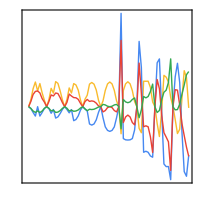

```mathematica
ticks={{{{0.,MaTeX["0"],ts},{-0.2,MaTeX["-0.2"],ts},{+0.2,MaTeX["+0.2"],ts}},Join[Table[{2i/100,MaTeX[If[(val=min+inc*i/100)≥0,"",""]<>ToString[NumberForm[val,{2,1}]]],ts[[2]]*{6,1}},{i,{20,40,60,80}}],{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{0.8,MaTeX["0.8"],ts},{1,MaTeX["1.0"],ts}},Table[{t,MaTeX[ToString[t]],ts},{t,10,40,10}],{{1.175,MaTeX["\\chi/\\pi"],.0}}],{None}}};
p[1]=ListPlot[{Vparas,Vperps,Vperps+Vparas,Us},GridLines->None,PlotLegends->Placed[{MaTeX["\\mathcal D_\\parallel/V_\\parallel"],MaTeX["\\mathcal D_\\perp/V_\\perp"],MaTeX["\\mathcal D_\\parallel/V_\\parallel+\\mathcal D_\\perp/V_\\perp"],MaTeX["\\mathcal D_U/U"]},{Left,Center}],FrameStyle->Black,FrameTicks->ticks,DataRange->{0.8,1.2}]
```

```mathematica
Export["cut_chi.png",p[1],ImageResolution->400]
```

```mathematica
ticks={{{{0.,MaTeX["0"],ts},{-0.2,MaTeX["-0.2"],ts},{+0.2,MaTeX["+0.2"],ts}},Join[Table[{2i/100,MaTeX[If[(val=min+inc*i/100)≥0,"",""]<>ToString[NumberForm[val,{2,1}]]],ts[[2]]*{6,1}},{i,{20,40,60,80}}],{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{0.8,MaTeX["0.8"],ts},{1,MaTeX["1.0"],ts}},Table[{t,MaTeX[ToString[t]],ts},{t,10,40,10}],{{1.175,MaTeX["g/t"],.0}}],{None}}};
p[2]=ListPlot[{Vparas,Vperps,Vperps+Vparas,Us},GridLines->None,(*PlotLegends->Placed[{MaTeX["\\mathcal D_\\parallel/V_\\parallel"],MaTeX["\\mathcal D_\\perp/V_\\perp"],MaTeX["\\mathcal D_\\parallel/V_\\parallel+\\mathcal D_\\perp/V_\\perp"],MaTeX["\\mathcal D_U/U"]},{Left,Center}],*)FrameStyle->Black,FrameTicks->ticks,DataRange->{0.8,1.2}]
```

-Graphics-

```mathematica
Export["cut_g.png",p[2],ImageResolution->400]
```

```mathematica
ListDensityPlot[{ggvals,chivals,Abs[absU[[All,1]]]^2-Abs[absV[[All,1]]]^2}ᵀ,PlotLegends->Automatic,PlotRange->{0,1}]
```

```mathematica
ListDensityPlot[{ggvals,chivals,Abs[absV[[All,1]]]}ᵀ,PlotLegends->Automatic,PlotRange->{0,1}]
```

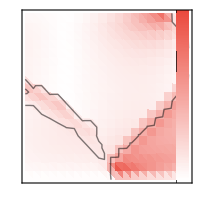

```mathematica
data=Abs[absU[[All,2]]/absU[[All,1]]];
max = 1.;
min = 0.;
inc=(max-min);
ths=Thickness[.003];
ts=0.02*{1,1/GoldenRatio};
bs=20;
line=Partition[Flatten[{Table[{1.85,2i/100,min+i*inc},{i,0,100}],Table[{2,2i/100,min+i*inc},{i,0,100}]}],3];
line=ListDensityPlot[line,ColorFunction->"GoogleGradientWhiteRed",PlotRangePadding->0];
ticks={{{{0.0,MaTeX["0"],ts},{1.0,MaTeX["1"],ts},{1.8,Rotate[MaTeX["\\chi/\\pi"],π/2],ts*0}},Join[Table[{2i/100,MaTeX[If[(val=min+inc*i/100)≥0,"",""]<>ToString[NumberForm[val,{2,1}]]],ts[[2]]*{6,1}},{i,{20,40,60,80}}],{{1.9,MaTeX["\\geq1"],0}}]},{Join[{{0,MaTeX["0"],ts},{1,MaTeX["1"],ts}},Table[{t,MaTeX[ToString[t]],ts},{t,10,40,10}],{{1.8,MaTeX["g/t"],.0}}],{None}}};
p[1]=Show[ListDensityPlot[{ggvals,chivals/π,data}ᵀ,PlotRange->Full,FrameTicks->ticks,InterpolationOrder->1,ClippingStyle->mygray,ColorFunctionScaling->False,ColorFunction->(ColorData["GoogleGradientWhiteRed"][Rescale[#,{min,max}]]&),GridLines->{{1.85},{}},FrameStyle->Black,GridLinesStyle->Black,PlotRangePadding->0],pCC2,line,ImagePadding->(ip={{20,25},{20,2}})]
```

```mathematica
data=Abs[absV[[All,2]]/absV[[All,1]]];
max = 1;
min = Min[data];
inc=(max-min);
ths=Thickness[.003];
ts=0.02*{1,1/GoldenRatio};
bs=20;
line=Partition[Flatten[{Table[{1.85,2i/100,min+i*inc},{i,0,100}],Table[{2,2i/100,min+i*inc},{i,0,100}]}],3];
line=ListDensityPlot[line,ColorFunction->"GoogleGradientWhiteRed",PlotRangePadding->0];
ticks={{{{0.0,MaTeX["0"],ts},{1.0,MaTeX["1"],ts},{1.8,Rotate[MaTeX["\\chi/\\pi"],π/2],ts*0}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{0,MaTeX["0"],ts},{1,MaTeX["1"],ts}},Table[{t,MaTeX[ToString[t]],ts},{t,10,40,10}],{{1.8,MaTeX["g/t"],.0}}],{None}}};
p[2]=Show[ListDensityPlot[{ggvals,chivals/π,data}ᵀ,PlotRange->{min,max},FrameTicks->ticks,ClippingStyle->myred,ColorFunctionScaling->False,ColorFunction->(ColorData["GoogleGradientWhiteRed"][Rescale[#,{min,max}]]&),GridLines->{{},{}},FrameStyle->Black,GridLinesStyle->Black,PlotRangePadding->0],pCC2,ImagePadding->ip]
```

-Graphics-

```mathematica
data=Abs[absU[[All,3]]/absU[[All,1]]];
p[3]=Show[ListDensityPlot[{ggvals,chivals/π,data}ᵀ,PlotRange->{min,max},FrameTicks->ticks,ClippingStyle->myred,ColorFunctionScaling->False,ColorFunction->(ColorData["GoogleGradientWhiteRed"][Rescale[#,{min,max}]]&),GridLines->{{},{}},FrameStyle->Black,GridLinesStyle->Black,PlotRangePadding->0],pCC2,ImagePadding->ip]
```

-Graphics-

```mathematica
data=Abs[absV[[All,3]]/absV[[All,1]]];
p[4]=Show[ListDensityPlot[{ggvals,chivals/π,data}ᵀ,PlotRange->{min,max},FrameTicks->ticks,ClippingStyle->myred,ColorFunctionScaling->False,ColorFunction->(ColorData["GoogleGradientWhiteRed"][Rescale[#,{min,max}]]&),GridLines->{{},{}},FrameStyle->Black,GridLinesStyle->Black,PlotRangePadding->0],pCC2,ImagePadding->ip]
```

-Graphics-

```mathematica
data=Abs[absU[[All,4]]/absU[[All,1]]];
p[5]=Show[ListDensityPlot[{ggvals,chivals/π,data}ᵀ,PlotRange->{min,max},FrameTicks->ticks,ClippingStyle->myred,ColorFunctionScaling->False,ColorFunction->(ColorData["GoogleGradientWhiteRed"][Rescale[#,{min,max}]]&),GridLines->{{},{}},FrameStyle->Black,GridLinesStyle->Black,PlotRangePadding->0],pCC2,ImagePadding->ip]
```

-Graphics-

```mathematica
data=Abs[absV[[All,4]]/absV[[All,1]]];
p[6]=Show[ListDensityPlot[{ggvals,chivals/π,data}ᵀ,PlotRange->{min,max},FrameTicks->ticks,ClippingStyle->myred,ColorFunctionScaling->False,ColorFunction->(ColorData["GoogleGradientWhiteRed"][Rescale[#,{min,max}]]&),GridLines->{{},{}},FrameStyle->Black,GridLinesStyle->Black,PlotRangePadding->0],pCC2,ImagePadding->ip]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/andreas/Desktop

```mathematica
Table[Export["derivatives"<>ToString[i]<>".png",p[i],ImageResolution->400],{i,1,6}]
```

{derivatives1.png,derivatives2.png,derivatives3.png,derivatives4.png,derivatives5.png,derivatives6.png}

```mathematica
ListPlot[{{ggvals,Us}ᵀ,{ggvals,Vparas}ᵀ,{ggvals,Vperps}ᵀ,{ggvals,(Vperps+Vparas)}ᵀ}]
```

```mathematica
ListPlot[{{ggvals,fermiVelocity[[All,1]]}ᵀ,{ggvals,fermiVelocity[[All,2]]}ᵀ}]
```

```mathematica
ListPlot[{{ggvals,fermiAcc[[All,1]]}ᵀ,{ggvals,fermiAcc[[All,2]]}ᵀ}]
```

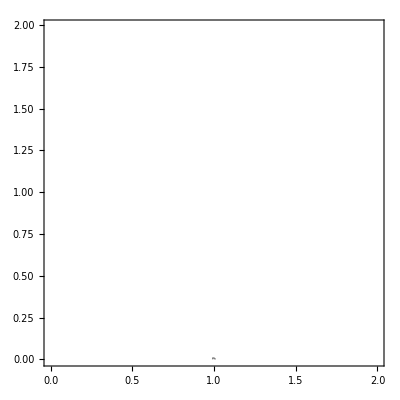

```mathematica
<<MaTeX`
(*Manipulate[plots[[i]],{i,1,Length[plots],1}]*)
pCC2=ListContourPlot[{ggvals,chivals/π,cc}//Transpose,InterpolationOrder->1,Contours->1,ContourShading->None,PlotRangePadding->0,FrameLabel->MaTeX[{"g/t","\\chi/\\pi"}]]
```

```mathematica
Manipulate[{Show[pCC2,Epilog->Inset[Graphics[Disk[{0,0},.02],PlotRange->{{-1,1},{-1,1}}],{ggvals[[ii]],chivals[[ii]]/π}]],bandfigs[[ii]]},{ii,1,Length[bandfigs],1}]
```

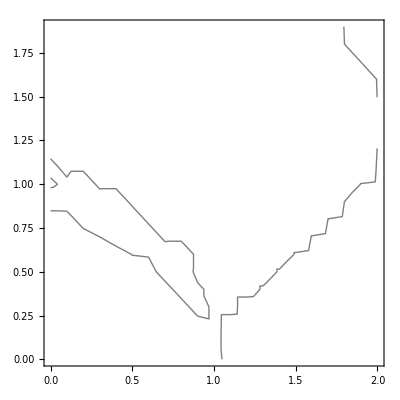

```mathematica
pCC2=ListContourPlot[{ggvals,chivals/π,fermiMomenta}//Transpose,InterpolationOrder->1,Contours->1,PlotLegends->Automatic,ContourShading->None,PlotRangePadding->0,FrameLabel->MaTeX[{"g/t","\\chi/\\pi"}]]
```

```mathematica
pPol=ListDensityPlot[{ggvals,chivals/π,polarization}//Transpose,InterpolationOrder->2,PlotLegends->Automatic,ColorFunction->"GoogleGradientWhiteRed",GridLines->None,PlotRangePadding->0,FrameLabel->MaTeX[{"g/t","\\chi/\\pi"}],ClippingStyle->mygray,PlotRange->(PR=Max[polarization]*{-1,1})]
```

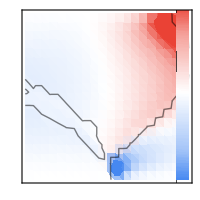

```mathematica
max=-Min[Vparas];
min=-max;
inc=(max-min);
ths=Thickness[.003];
ts=0.02*{1,1/GoldenRatio};
bs=20;
line=Partition[Flatten[{Table[{1.85,2i/100,min+i*inc},{i,0,100}],Table[{2,2i/100,min+i*inc},{i,0,100}]}],3];
line=ListDensityPlot[line,ColorFunction->"GoogleGradient",PlotRangePadding->0];
ticks={{{{0.0,MaTeX["0"],ts},{1.0,MaTeX["1"],ts},{1.8,Rotate[MaTeX["\\chi/\\pi"],π/2],ts*0}},Join[Table[{2i/100,MaTeX[If[(val=min+inc*i/100)≥0,"+",""]<>ToString[NumberForm[Round[val,.1],{3,1}]]],ts[[2]]*{5,1}},{i,{20,40,60,80}}],{{1.9,MaTeX["\\geq 0.2"]"",{0.,0}}},{{0.1,MaTeX["\\leq 0.2"]"",{0.,0}}}]},{Join[{{0,MaTeX["0"],ts},{1,MaTeX["1"],ts}},Table[{t,MaTeX[ToString[t]],ts},{t,10,40,10}],{{1.8,MaTeX["g/t"],.0}}],{None}}};
pHub=Show[ListDensityPlot[{ggvals,chivals/π,Us}//Transpose,InterpolationOrder->1,ColorFunctionScaling->False,ColorFunction->(ColorData["GoogleGradient"][Rescale[#,{min,max}]]&),ClippingStyle->{myblue,myred},GridLines->None,PlotRangePadding->0,PlotRange->{min,max}],pCC2,line,GridLines->{{1.85},{}},GridLinesStyle->Black,FrameStyle->Black,FrameTicks->ticks,ImagePadding->(ip={{20,32},{20,2}})]
```

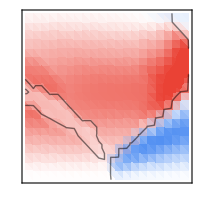

```mathematica
inc=(max-min);
ths=Thickness[.003];
ts=0.02*{1,1/GoldenRatio};
bs=20;
ticks={{{{0.0,MaTeX["0"],ts},{1.0,MaTeX["1"],ts},{1.8,Rotate[MaTeX["\\chi/\\pi"],π/2],ts*0}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{0,MaTeX["0"],ts},{1,MaTeX["1"],ts}},Table[{t,MaTeX[ToString[t]],ts},{t,10,40,10}],{{1.8,MaTeX["g/t"],.0}}],{None}}};
pNNpara=Show[ListDensityPlot[{ggvals,chivals/π,Vparas}ᵀ,InterpolationOrder->1,GridLines->None,ColorFunctionScaling->False,ColorFunction->(ColorData["GoogleGradient"][Rescale[#,{min,max}]]&),ClippingStyle->{myblue,myred},PlotRangePadding->0,ClippingStyle->mygray,PlotRange->{min,max}],pCC2,GridLines->{{},{}},GridLinesStyle->Black,FrameStyle->Black,FrameTicks->ticks]
```

```mathematica
min=Min[Vperps];
max=Abs[min];
inc=(max-min);
ths=Thickness[.003];
ts=0.02*{1,1/GoldenRatio};
bs=20;
line=Partition[Flatten[{Table[{1.85,2i/100,min+i*inc},{i,0,100}],Table[{2,2i/100,min+i*inc},{i,0,100}]}],3];
line=ListDensityPlot[line,ColorFunction->"GoogleGradient",PlotRangePadding->0];
ticks={{{{0.0,MaTeX["0"],ts},{1.0,MaTeX["1"],ts},{1.8,Rotate[MaTeX["\\chi/\\pi"],π/2],ts*0}},Join[Table[{2i/100,MaTeX[If[(val=min+inc*i/100)≥0,"+",""]<>ToString[NumberForm[val,{3,2}]]],ts[[2]]*{5,1}},{i,{20,40,60,80}}],{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{0,MaTeX["0"],ts},{1,MaTeX["1"],ts}},Table[{t,MaTeX[ToString[t]],ts},{t,10,40,10}],{{1.8,MaTeX["g/t"],.0}}],{None}}};
pNNperp=Show[ListDensityPlot[{ggvals[[;;-2]],chivals[[;;-2]]/π,Vperps}//Transpose,InterpolationOrder->1,ColorFunction->"GoogleGradient",PlotRangePadding->0,GridLines->None,ClippingStyle->mygray,PlotRange->{min,max}],pCC2,line,GridLines->{{1.85},{}},GridLinesStyle->Black,FrameStyle->Black,FrameTicks->ticks]
```

```mathematica
(*min=Min[Vparas[[;;-2]]+Vperps];
max=Abs[min];*)
inc=(max-min);
ths=Thickness[.003];
ts=0.02*{1,1/GoldenRatio};
bs=20;
line=Partition[Flatten[{Table[{1.85,2i/100,min+i*inc},{i,0,100}],Table[{2,2i/100,min+i*inc},{i,0,100}]}],3];
line=ListDensityPlot[line,ColorFunction->"GoogleGradient",PlotRangePadding->0];
ticks={{{{0.0,MaTeX["0"],ts},{1.0,MaTeX["1"],ts},{1.8,Rotate[MaTeX["\\chi/\\pi"],π/2],ts*0}},Join[Table[{2i/100,MaTeX[If[(val=min+inc*i/100)≥0,"+",""]<>ToString[NumberForm[val,{3,2}]]],ts[[2]]*{5,1}},{i,{20,40,60,80}}],{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{0,MaTeX["0"],ts},{1,MaTeX["1"],ts}},Table[{t,MaTeX[ToString[t]],ts},{t,10,40,10}],{{1.8,MaTeX["g/t"],.0}}],{None}}};
pNNSum=Show[ListDensityPlot[{ggvals[[;;-2]],chivals[[;;-2]]/π,(Vparas[[;;-2]]+Vperps)}//Transpose,InterpolationOrder->1,GridLines->None,ColorFunction->"GoogleGradient",PlotRangePadding->0,ClippingStyle->mygray,PlotRange->{min,max}],pCC2,line,GridLines->{{1.85},{}},GridLinesStyle->Black,FrameStyle->Black,FrameTicks->ticks]
```

```mathematica
ubosnaive[m_,g_,χ_,k_]=+(2 uu[m,g,χ,k]^2*vv[m,g,χ,k]^2-(uu[m,g,χ,k]^2-vv[m,g,χ,k]^2)^2);
ubosnaivelist=Table[ubosnaive[1.0,ggvals[[ii]],chivals[[ii]]/π,fermiMomenta[[ii]]],{ii,1,Length[ggvals]}];
ListDensityPlot[{ggvals,chivals/π,ubosnaivelist}ᵀ,PlotLegends->Automatic,ColorFunction->"GoogleGradient",PlotRange->Max[ubosnaivelist]*{-1,1},ClippingStyle->mygray]
```

```mathematica
sol=k/.Solve[bands[mm,N[gg],chi,0.25π][[2]]==bands[mm,N[gg],chi,k][[2]],k];
```

```mathematica
bb=Partition[Flatten[Table[{gee,schi/π,3-Dimensions[DeleteDuplicates[Abs[Im[sol/.{gg->N[gee],chi->N[schi]}]]]][[1]]},{gee,0.001,2,0.005},{schi,0,1.99π,0.005π}]//Quiet],3];
```

```mathematica
Intersection[Position[ggvals,n_ /; n==1],Position[chivals/π,n_ /; n==1]]
```

```mathematica
pnnpara=Show[pNNpara]
pnnperp=Show[pNNperp]
pnnsum=Show[pNNSum]
phub=Show[pHub]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["Drudeweight_phasediagram_NNpara"<>".png",pnnpara,ImageResolution->400]
Export["Drudeweight_phasediagram_NNperp"<>".png",pnnperp,ImageResolution->400]
Export["Drudeweight_phasediagram_NNsum"<>".png",pnnsum,ImageResolution->400]
Export["Drudeweight_phasediagram_Hub"<>".png",phub,ImageResolution->400]
```

```mathematica
pCC=ListContourPlot[bb,PlotRangePadding->0,InterpolationOrder->1,PlotLegends->Automatic,ContourShading->None,Contours->1]
```

```mathematica
(** SOME DOUBLE CHECKS THAT EVERYTHING IS CONSISTENT **)

(* Formula taken from Manon's PRB Rapid *)
D1Manon[ρ_,L_]=π/L^2*(Csc[π/(2L)]^2*Sin[(π ρ)/2]^2)/(1+2*Cos[π/L])*Cos[π/L]*(Cos[π/L]-Cos[π ρ]);
D0Manon[ρ_,L_]=π/L*Cos[π/2(1-ρ)]*Cot[π/(2L)];(* WATCHOUT: factor 1/2 is missing since D0 = Subscript[v, F] for noninteracting models... *)
Limit[D1Manon[ρ,L],L->∞](* Manons PRB Limit *)
```

```mathematica
FullSimplify[DrudePara[m,g,χ,k,l,L,Vpar]+DrudePerp[m,g,χ,k,l,L,Vperp]/.{χ->π,m->1,g->1}](* What I get from the generalized model *)
```

```mathematica
F1[k,l]=DrudePerp[1,1,π,k,l,L,Vperp]/Vperp//Simplify (* The integrals over k and l can be reduced to something more simple, see below... *)
```

```mathematica
Plot[Sin[k/2]^3/(1-Cos[k])^(3/2)*2^(3/2),{k,-π,π}](* this is Sign[k]*)
```

```mathematica
(* take the sums explicitly *)
∑_(m=-L/2)^(-L/2(1-ρ)-1) ∑_(n=-L/2)^(-L/2(1-ρ)-1) π/L^2*Cos[(2π)/L(m+n)/2]*Sin[(2π)/L(m-n)/2]^2+∑_(m=L/2(1-ρ))^(L/2-1) ∑_(n=L/2(1-ρ))^(L/2-1) π/L^2*Cos[(2π)/L(m+n)/2]*Sin[(2π)/L(m-n)/2]^2-∑_(m=-L/2)^(-L/2(1-ρ)-1) ∑_(n=L/2(1-ρ))^(L/2-1) π/L^2*Cos[(2π)/L(m+n)/2]*Sin[(2π)/L(m-n)/2]^2-∑_(m=L/2(1-ρ))^(L/2-1) ∑_(n=-L/2)^(-L/2(1-ρ)-1) π/L^2*Cos[(2π)/L(m+n)/2]*Sin[(2π)/L(m-n)/2]^2 ;
```

```mathematica
FullSimplify[%]
```

```mathematica
Limit[%,L->∞]
```

```mathematica
Simplify[(2 π Cos[π/L] (Cos[π/L]-Cos[π ρ]) Sin[(π ρ)/2]^2)/(L^2 (-Cos[π/L]+Cos[(2 π)/L]))+D1Manon[ρ,L]](* The two expressions are identical *)
```